```mathematica
(*ep=6.7;β=0.75;γ=0.086;*)
xmin=-50;xmax=50;maxtime=400;δ=0; 
α=0.2;γt=0.02;sg =0.0036;
eps=0.15;eps=0.163;
d1[x_]=Which[x<0,1,True,eps];
f[v_]=v(1-v)(v-α);
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{InterpolatingFunction[{{0., 400.}, {-50., 50.}}, <>],InterpolatingFunction[{{0., 400.}, {-50., 50.}}, <>]}

-Graphics3D-

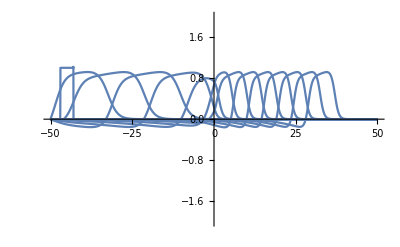

```mathematica
{V1,W1}=NDSolveValue[{D[u[t, x], t] == d1[x] D[u[t, x], x, x]+f[u[t,x]] - w[t,x], D[w[t, x], t] ==(sg u[t, x] - γt w[t, x]), 
u[0, x] == Which[Abs[x+45] <=2,1,True, 0], 
w[0, x] ==0,
u[t, xmin] == 0, 
u[t, xmax] == 0}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}]
Plot3D[V1[t,x], {t, 0, maxtime}, {x, xmin, xmax},PlotRange->{-2,2},AxesLabel->{"time","space"},Mesh->All]
Plot[Table[V1[t,x],{t,0,maxtime,30}],{x,xmin,xmax},PlotRange->{-2,2}]
```

```mathematica
Animate[Plot[{V1[t,x],W1[t,x],d1[x]},{x,xmin,xmax},PlotRange->{{xmin,xmax},{-2,2}}],{t,0,maxtime},AnimationRunning->False,AnimationRepetitions->1]
```